```mathematica
PacletInstall["https://wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

## Some problem-solving (QuantumState and QuantumBasis)

- create a random 2D pure state
- visualize the Bloch vector
- find the corresponding Bloch spherical and also Cartesian coordinates
- find the state vector in the computational and also Pauli-X basis

- create qubit trine (define as: 0, -1/20-(√3)/2 1,-1/20+(√3)/2 1 
- find their state vector in Pauli-Y basis

- Create a superposition of Bell states 1/(√3)Φ_+-√(2/3)Ψ_-.
- Find its formula.
- After tracing out the 2nd qubit, find the corresponding state of qubit-1. Test if it is a mixed state. 
- Purify the qubit-1 state obtained in the previous state. Show that if tracing out the ancillary qubit from the purified state, one recovers the same state.

- generate two random mixed state in 2D, and calculate their Bures distance

- show that a Werner state in d=2 is separable if p>=1/2, and entangled if p<1/2
(Hint: you can directly use QuantumEntangledQ, or PPT criterion. The PPT criterion stats that if ρ is separable then all the eigenvalues of the partial transpose of ρ are non-negative. In other words, if the partial transpose of ρ has a negative eigenvalue, ρ is guaranteed to be entangled)

- Show the Schmidt decomposition of this state 1/(√6)(00+01+√2 10-√2 11)
- find the Schmidt coefficients, too.

- generate the W state of 4 qubits. 
- bi-partition the corresponding state into a bipartite system of 2D and 8D (dimensions 2x8)
- find the corresponding Schmidt decomposition and Schmidt coefficients

- given the start graph of 4 vertices (S_4), find the corresponding cluster state. Test if qubit-1 and 2 are entangled or not. Also test, if the overall state is separable or not.

- Given a Werner state with d=2, show that it can be written as a convex combination as follows: (1-λ)/4 I+λΨ_-Ψ_- with λ∈[0,4/3] (Hint: use the replacement rule λ->(1-4p/3))
- find the domain in which ρ is entangled (Hint: PPT criterion stats that if ρ is separable then all the eigenvalues of the partial transpose of ρ are non-negative. In other words, if the partial transpose of ρ has a negative eigenvalue, ρ is guaranteed to be entangled)

## QuantumOperators

The most important pattern to remember is QuantumOperator[arg,order]

```mathematica
QuantumOperator["X"]
```

QuantumOperator[…]

Note by default, the order is set as {1}, or {1,2}, or {1,2,...} (depending on the operator)

Controlled-H

```mathematica
QuantumOperator["CH"]
```

QuantumOperator[…]

```mathematica
%["ControlOrder"]
```

{1}

```mathematica
%%["TargetOrder"]
```

{2}

Permutation, given a cycle

```mathematica
QuantumOperator[{"Permutation",Cycles[{{1,3,2}}]}]
```

QuantumOperator[…]

```mathematica
QuantumCircuitOperator[%]["Diagram"]
```

-Graphics-

Another way of finding out what qubit goes where after a permutation, given a cycle:

```mathematica
Permute[{1,2,3},Cycles[{{1,3,2}}]]
```

{2,3,1}

Make sure to use order (makes ur life easier)

```mathematica
QuantumOperator["X",{1,2}]==QuantumOperator["X"]@QuantumOperator["X",{2}]==QuantumTensorProduct[QuantumOperator["X"],QuantumOperator["X"]]
```

Some arithmetic/operations on operators:

```mathematica
Exp[-ⅈ θ/2 QuantumOperator["X"]]
```

```mathematica
%==QuantumOperator[{"RX",θ}]
```

Taking sqrt of an operator (note there are different way of doing that)

```mathematica
Sqrt[QuantumOperator["X"]]
```

QuantumOperator[…]

```mathematica
%==QuantumOperator["SX"]
```

True

```mathematica
%%==QuantumOperator[Sqrt@"X"]
```

True

Addition/subtraction

```mathematica
QuantumOperator["T"+"X"]
```

```mathematica
%==QuantumOperator["T"]+QuantumOperator["X"]
```

```mathematica
QuantumOperator["YY"+"XX"+"ZZ"]
```

```mathematica
QuantumOperator["XX"+"YY"+"ZZ"]==Total[QuantumOperator/@{"XX","YY","ZZ"}]
```

```mathematica
QuantumOperator[{"R",θ,"XX"+"YY"+"ZZ"}]
```

```mathematica
FullSimplify[%==QuantumOperator[{"R",θ,"XX"}]@QuantumOperator[{"R",θ,"YY"}]@QuantumOperator[{"R",θ,"ZZ"}]]
```

Note that above operation (separating the exponentials, ie Exp[ABC]=Exp[A]Exp[B]Exp[C]) can be done only if the operators commute (which is the case here)

Ising coupling Exp[-ⅈ θ/2 (X_1 X_2+X_2 X_3)]

```mathematica
QuantumOperator[{"R",θ,{"XX"->{1,2},"XX"->{2,3}}}]
```

QuantumOperator[…]

One can define controlled-operators with many control and target

```mathematica
ctrl1={2};
ctrl0={4,5};
cu=QuantumOperator[{"C",{"X"->{1},"Y"->{3}},ctrl1,ctrl0}]
```

```mathematica
QuantumCircuitOperator[cu]["Diagram"]
```

Ising-type of interactions and their Trotter-Suzuki decomposition (4th order)

```mathematica
op=Table[QuantumOperator["XX",{i,i+1}],{i,5}];
```

```mathematica
qc=QuantumCircuitOperator[{"Trotterization",op,4,1}];
```

```mathematica
qc["Diagram","ShowGateLabels"->False]
```

```mathematica
#["Label"]&/@qc["Operators"]
```

An operator is a tensor flow with input and output:

```mathematica
QuantumOperator["H",{2,3}]["Diagram"]
```

## Problem solving (QuantumOperator)

- create a uniform superposition of 8-qubits using QuantumState only
- create the same state, by applying Hadamard operators on a register state

- Explore why Pauli-Z is also called phase flip

- Create the rotation in the Bloch sphere, around an arbitrary unit vector n⃗ (usually this gate is denoted as R_(n⃗)(θ)=Exp[-ⅈ θ/2 n⃗.σ⃗]

- create a canonical gate, which is a 3-parameter quantum logic gate that acts on two qubits
Exp[-ⅈ π/2 (t_x XX+t_y YY+t_z ZZ)]

- create Givens gate: Exp[-ⅈ θ/2 (YX-XY)]

- Pauli power gates are σ_i^t. Show that they are the same as corresponding rotation with the angle π t

- given a [fractional] phase shift gate (ie a phase operator an angle 2π/2^n), show that P_1=Z, P_2=S and P_3=T

- a global phase in front of a quantum state is not observable. Apply a global phase to a 2D random quantum state, and test if it is the same as the original one

- create the inverse V gate (V gate is √X; note it is not Hermitian)

- test these relations
Z = H X H
NOT  = R_x(π)Ph(π/2)
NOT = R_y(π)R_z(π)Ph(π/2)
√NOT=R_x(π/2)Ph(π/4)

Find ZYZ decomposition of a random unitary operator

Create Berkeley B operator: Exp[ⅈ π/8 (2 XX + YY)]

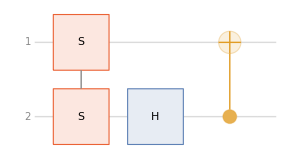
Create the following circuit using only operators (circuit for magic basis transformation)
-Graphics-

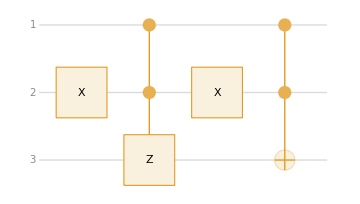
Create the following circuit using only operators (this circuit is also called Margolus gate)
-Graphics-

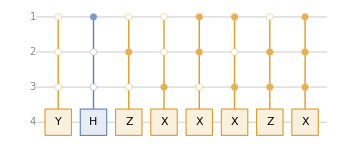
Create the following circuit using only operators (this type of circuit is also called multiplexed gates)
-Graphics-

## QuantumMeasurementOperator

Either usual PVMs or generic POVMs
Think of it very similar to quantum operator (given basis, and order)

```mathematica
qm=QuantumMeasurementOperator[{1,3}][QuantumState[{"RandomPure",3}]]
```

```mathematica
qm["ProbabilityPlot"]
```

```mathematica
qm["Probabilities"]
```

```mathematica
qm["StateAssociation"]
```

```mathematica
QuantumMeasurementOperator[{1,2,3}][QuantumState[{"RandomPure",3}]]
```

```mathematica
%["ProbabilityPlot"]
```

POVM:

```mathematica
states={QuantumState[-1/2{1,√3}],QuantumState[-1/2{1,-√3}],QuantumState["0"]};
{e1,e2,e3}=2/3#["Operator"]&/@states;
povm={e1,e2,e3};
```

```mathematica
PositiveSemidefiniteMatrixQ[#["Matrix"]]&/@povm
```

```mathematica
Total[povm]==QuantumOperator["I"]
```

```mathematica
qm=QuantumMeasurementOperator[povm][QuantumState["RandomPure"]]
```

```mathematica
qm["ProbabilityPlot"]
```